```mathematica
ClearAll["Global`*"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
colors=(("DefaultPlotStyle"/.(Method/.Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/.Directive[x_,__]:>x);
```

```mathematica
<<MaTeX`
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color}","\\definecolor{SCred}{rgb}{0.9,0.36,0.054}","\\definecolor{SCblue}{rgb}{0.365248,0.427802,0.758297}","\\definecolor{SCyellow}{rgb}{0.945109,0.593901,0}"}];
```

```mathematica
Needs["ErrorBarPlots`"];
```

```mathematica
Integerise[x_]:=If[Round[x]==x,ToString[Round@x]<>".0",ToString@x];
```

```mathematica
imported[k_]:= Import["braid_measures_K"<>ToString[Integerise[k]]<>".txt","Table"];
```

```mathematica
data[k_] := Pick[imported[k],Unitize@imported[k][[All,-1]],1]
```

```mathematica
data2[k_] := imported[k];
```

```mathematica
CTunfiltered[k_]:=Import["CT_content_K"<>ToString[Integerise[k]]<>".txt","Table"]
```

```mathematica
ct[k_]:=DeleteCases[Import["CT_content_K"<>ToString[Integerise[k]]<>".txt","Table"],{0,0,0,0,0,0,0,0,0}];
```

```mathematica
CT[k_]:=N@Mean[ct[k]/Total[Transpose[ct[k]]]];
```

```mathematica
writhe = Table[{{k,Mean[data[k][[All,1]]]},ErrorBar[StandardDeviation[data[k][[All,1]]]/Sqrt[Length[data[k][[All,1]]]]]},{k,0,12,0.2}];
```

```mathematica
complexity =  Table[{{k,Mean[data[k][[All,2]]/Log[3]]},ErrorBar[StandardDeviation[data[k][[All,2]]/Log[3]]/Sqrt[Length[data[k][[All,2]]/Log[3]]]]},{k,0,12,0.2}];
```

```mathematica
length =  Table[{{k,Mean[data[k][[All,3]]]},ErrorBar[StandardDeviation[data[k][[All,3]]]/Sqrt[Length[data[k][[All,3]]]]]},{k,0,12,0.2}];
```

```mathematica
rg = Table[{{k,Mean[imported[k][[All,4]]]/Sqrt[(9/6)*0.972^2]},ErrorBar[StandardDeviation[imported[k][[All,4]]/Sqrt[(9*0.972^2)/6]]/Sqrt[Length[imported[k][[All,4]]]]]},{k,0,12,0.2}];
```

```mathematica
cr =Table[{{k,Mean[imported[k][[All,5]]]},ErrorBar[StandardDeviation[imported[k][[All,5]]]/Sqrt[Length[imported[k][[All,5]]]]]},{k,0,12,0.2}];
```

```mathematica
cterr[k_]:=N[StandardDeviation[ct[k]/Total[Transpose[ct[k]]]]/Sqrt[Length[ct[k]/Total[Transpose[ct[k]]]]]];
```

```mathematica
Cmax = Table[{k,Max[data[k][[All,2]]]},{k,0,12,0.2}];
Lmax = Table[{k,Max[data[k][[All,3]]]},{k,0,12,0.2}];
```

```mathematica
ListPlot[Table[MovingAverage[complexity[[All,1]],i],{i,1,20}],PlotRange->All,Joined->False];
```

```mathematica
ListPlot[Table[MovingAverage[length[[All,1]],i],{i,1,8}],PlotRange->All,Joined->False];
```

```mathematica
N[complexity[[All,1,2]][[-1]]/length[[All,1,2]][[-1]]]
```

0.346025

```mathematica
N[0.77/2.22]
```

0.346847

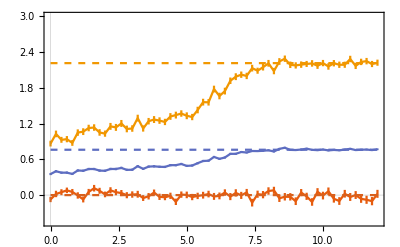

```mathematica
TMp = With[{XZ=400,YZ=300},Show[ErrorListPlot[{writhe,complexity,length},ImageSize->Automatic->{XZ,YZ},PlotRange->{{0,All},{-0.45,3}},Joined->True,PlotTheme->"Scientific",FrameTicks->Automatic,FrameTicksStyle->Directive[Black,14]],Plot[{0,0.7616247149434183,2.2162514584434407},{k,0,12},PlotStyle->Dashed,PlotTheme->"Scientific"],Epilog->{ Text[MaTeX["\\textcolor{SCyellow}{L}",FontSize->22],Scaled[{0.9,0.87}]],Text[MaTeX["\\textcolor{SCblue}{C}",FontSize->22],Scaled[{0.9,0.47}]],Text[MaTeX["\\textcolor{SCred}{W}",FontSize->22],Scaled[{0.9,0.27}]], Text[MaTeX["\\kappa",FontSize->22],Scaled[{0.95,0.05}]],Text[MaTeX["(a)",FontSize->28],Scaled[{0.5,0.9}]]}]]
```

```mathematica
Export["N10WCL.pdf",TMp];
```

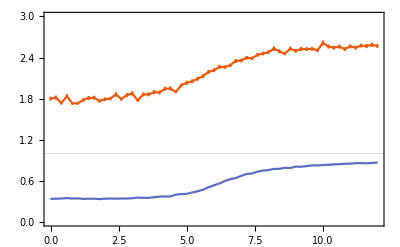

```mathematica
CRGRp = With[{XZ=400,YZ=300},Show[ErrorListPlot[{rg,cr},Joined->True,ImageSize->Automatic->{XZ,YZ},PlotRange->{{0,12},{0,3}},PlotTheme->"Scientific",FrameTicks->Automatic,FrameTicksStyle->Directive[Black,14],GridLines->{None,{1}}],Epilog->{ Text[MaTeX["\\textcolor{SCred}{\\widetilde{R}_g}",FontSize->22],Scaled[{0.9,0.75}]],Text[MaTeX["\\textcolor{SCblue}{C_R}",FontSize->22],Scaled[{0.9,0.22}]], Text[MaTeX["\\kappa",FontSize->22],Scaled[{0.95,0.05}]],Text[MaTeX["(b)",FontSize->28],Scaled[{0.5,0.9}]]}]]
```

```mathematica
Export["N10RGCR.pdf",CRGRp];
```

```mathematica
(*motifs = {"S","P","X","L_2","I_2","T_2","T_3","I_3","I_4"};*)
```

```mathematica
motifs1 = {MaTeX["S",FontSize->18],MaTeX["P",FontSize->18],MaTeX["X",FontSize->18],MaTeX["L_2",FontSize->18],MaTeX["I_2",FontSize->18],MaTeX["T_2",FontSize->18]};
```

```mathematica
motifs2 = {MaTeX["T_3",FontSize->18],MaTeX["I_3",FontSize->18],MaTeX["I_4",FontSize->18]};
```

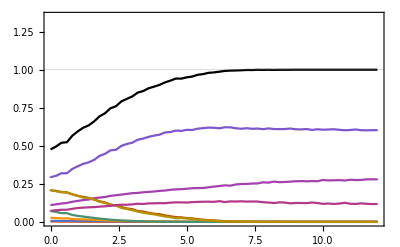

```mathematica
CTp = With[{XZ=400,YZ=300},Show[ErrorListPlot[Table[Table[{{k,CT[k][[j]]},ErrorBar[cterr[k][[j]]]},{k,0,12,0.2}],{j,1,9}],PlotRange->{{0,All},{0,1.35}},ImageSize->Automatic->{XZ,YZ},Joined->True,FrameTicks->Automatic,FrameTicksStyle->Directive[Black,14],PlotTheme->"Scientific",PlotLegends->{Placed[LineLegend[Table[colors[[i]],{i,1,6}],motifs1,LegendLayout->{"Row",2}],{Scaled[{0.05,0.87}],{0.05,0.5}}],Placed[LineLegend[Table[colors[[i]],{i,7,9}],motifs2,LegendLayout->{"Row",2}],{Scaled[{0.75,0.87}],{0.05,0.5}}]},GridLines->{None,{1}}],ListPlot[Table[{k,Total[Evaluate@CT[k][[{4,7,9}]]]},{k,0,12,0.2}],PlotRange->{{0,All},{0,1.1}},ImageSize->Automatic->{XZ,YZ},Joined->True,PlotStyle->Black],Epilog->{ Text[MaTeX["\\kappa",FontSize->22],Scaled[{0.95,0.05}]],Text[MaTeX["(c)",FontSize->28],Scaled[{0.5,0.9}]]}]]
```

```mathematica
Export["N10CT.pdf",CTp];
```

```mathematica
n = 10; m=4;
pplot[p_,vp_]:=Block[{i=p},polymers=Import["/home/jonas/Documents/Research/Circuit Topology/Multichain simulations/Four strands/N10M4 (final, do not touch)/Snapshots/K"<>ToString[i]<>".lammpstrj","Table"];
polfinal = polymers[[Length[polymers]-(n*m-1);;-1]];
pol[k_]:= BezierCurve[polfinal[[n*(k-1) +1;;n*k,4;;-1]]];
Graphics3D[{{Blend[{Blue,White},0.3],Tube[pol[1],0.5]},{Blend[{Blue,White},0.5],Tube[pol[2],0.5]},{Blend[{Yellow,White},0.7],Tube[pol[3],0.5]},{Blend[{Yellow,White},0.9],Tube[pol[4],0.5]}},Boxed->False,ViewPoint->vp]]
```

```mathematica
ptmp = With[{XZ=500,YZ=500/3},GraphicsGrid[{{pplot[0,{2.5516285792407194,-1.087338143201299,1.9382691649875508}],pplot[6,{0.8521925224794904,-0.7799413656823436,3.1804809967562457}],pplot[9,{3.2546984423998464,1.9015999290234211,0.75098942996485965}]}},Frame->None,ImageSize->Automatic->{XZ,YZ},Epilog->{Text[MaTeX["\\kappa = 0",FontSize->22],Scaled[{0,0.05}]],Text[MaTeX["\\kappa = 6",FontSize->22],Scaled[{0.5,0.05}]],Text[MaTeX["\\kappa = 9",FontSize->22],Scaled[{1,0.05}]]}]]
```

-Graphics-

### 1: Pseudo-Anosov; 2: reducible; 3: finite-order (periodic)

```mathematica
TNplot = With[{XZ=400,YZ=300},BarChart[Table[Sort[Tally[data[k][[All,-1]]]][[All,2]]/Total[Sort[Tally[data[k][[All,-1]]]][[All,2]]],{k,0,12,0.2}],ChartLayout->"Stacked",Frame->True,PlotRange->All,PlotRangePadding->{{-0.45,0.05},{0.001,0.0001}},BarOrigin->Bottom,BarSpacing->{0,0},AxesOrigin->{0,0},FrameTicksStyle->Directive[Black,14],ChartLabels->{Placed[Table[If[Mod[k,2]==0,Round[k],None],{k,0,12,0.2}],Axis],Automatic},Joined->True,ImageSize->Automatic->{XZ,YZ},PlotTheme->"Scientific",ChartStyle->{Directive[colors[[1]],Opacity[0.5]],Directive[colors[[2]],Opacity[0.5]],Directive[White]},Epilog->{ Text[MaTeX["\\kappa",FontSize->22],Scaled[{0.95,0.05}]],Text[MaTeX["IC",FontSize->22],Scaled[{0.05,0.93}]],Text[MaTeX["\\textcolor{black}{\\bf PA}",FontSize->18],Scaled[{0.68,0.045}]],Text[MaTeX["\\textcolor{black}{\\bf RE}",FontSize->18],Scaled[{0.73,0.15}]],Text[MaTeX["\\textcolor{black}{\\bf FO}",FontSize->18],Scaled[{0.5,0.75}]],Text[MaTeX["(d)",FontSize->28],Scaled[{0.5,0.9}]],Inset[pplot[0,{2.5516285792407194,-1.087338143201299,1.9382691649875508}],Scaled[{0.15,0.4}],ImageScaled[{0.5,0.5}],15],Inset[pplot[6,{0.8521925224794904,-0.7799413656823436,3.1804809967562457}],Scaled[{0.5,0.4}],ImageScaled[{0.5,0.5}],15],Inset[pplot[9,{3.2546984423998464,1.9015999290234211,0.75098942996485965}],Scaled[{0.85,0.4}],ImageScaled[{0.5,0.5}],15]}]]
```

-Graphics-

```mathematica
ppgrid = Grid[{{TMp,CRGRp},{CTp,TNplot}},Spacings->{0.5,0.5}]
```

-Graphics-

```mathematica
Export["N10gridplot.pdf",ppgrid,"AllowRasterization"->True,ImageSize->360,ImageResolution->600];
```

```mathematica
CK[k_,s_]:=Transpose[{ConstantArray[k,Length@data[k][[All,s]]] ,data[k][[All,s]]}];
```

```mathematica
dpW = With[{XZ=200,YZ=200},SmoothDensityHistogram[Flatten[Table[CK[k,1],{k,0,12,0.2}],1],Automatic,"PDF",PlotRange->{{0,12},{-5,5}},PlotRangePadding->None,Frame->True,PlotTheme->"Scientific",FrameTicksStyle->Directive[Black,12],ColorFunction->"SunsetColors",ImageSize->Automatic->{XZ,YZ},Epilog->{Text[MaTeX["\\textcolor{white}{\\bf W}",FontSize->18],Scaled[{0.1,0.9}]],Text[MaTeX["\\textcolor{white}{\\bf \\kappa}",FontSize->18],Scaled[{0.9,0.07}]]}]];
```

```mathematica
dpC = With[{XZ=200,YZ=200},SmoothDensityHistogram[Flatten[Table[CK[k,2],{k,0,12,0.2}],1],Automatic,"PDF",PlotRange->{{0,12},{0,2}},Frame->True,PlotRangePadding->None,PlotTheme->"Scientific",FrameTicksStyle->Directive[Black,12],ColorFunction->"SunsetColors",ImageSize->Automatic->{XZ,YZ},Epilog->{Text[MaTeX["\\textcolor{white}{\\bf C}",FontSize->18],Scaled[{0.1,0.9}]],Text[MaTeX["\\textcolor{white}{\\bf \\kappa}",FontSize->18],Scaled[{0.9,0.07}]]}]];
```

```mathematica
dpL = With[{XZ=200,YZ=200},SmoothDensityHistogram[Flatten[Table[CK[k,3],{k,0,12,0.2}],1],Automatic,"PDF",PlotRange->{{0,12},{0,7}},Frame->True,PlotRangePadding->None,PlotTheme->"Scientific",FrameTicksStyle->Directive[Black,12],ColorFunction->"SunsetColors",ImageSize->Automatic->{XZ,YZ},Epilog->{Text[MaTeX["\\textcolor{white}{\\bf L}",FontSize->18],Scaled[{0.1,0.9}]],Text[MaTeX["\\textcolor{white}{\\bf \\kappa}",FontSize->18],Scaled[{0.9,0.07}]]}]];
```

```mathematica
dpGR = With[{XZ=200,YZ=200},SmoothDensityHistogram[Flatten[Table[CK[k,4],{k,0,12,0.2}],1],Automatic,"PDF",PlotRange->{{0,12},{1.5,3}},Frame->True,FrameTicksStyle->Directive[Black,12],PlotTheme->"Scientific",PlotRangePadding->None,ColorFunction->"SunsetColors",ImageSize->Automatic->{XZ,YZ},Epilog->{Text[MaTeX["\\textcolor{white}{\\bf \\widetilde{R}_g}",FontSize->18],Scaled[{0.1,0.9}]],Text[MaTeX["\\textcolor{white}{\\bf \\kappa}",FontSize->18],Scaled[{0.9,0.07}]]}]];
```

```mathematica
dpCR= With[{XZ=200,YZ=200},SmoothDensityHistogram[Flatten[Table[CK[k,5],{k,0,12,0.2}],1],Automatic,"PDF",PlotRange->{{0,12},{0,1}},Frame->True,ColorFunction->"SunsetColors",PlotTheme->"Scientific",PlotRangePadding->None,FrameTicksStyle->Directive[Black,12],ImageSize->Automatic->{XZ,YZ},Epilog->{Text[MaTeX["\\textcolor{white}{\\bf C_R}",FontSize->18],Scaled[{0.1,0.9}]],Text[MaTeX["\\textcolor{white}{\\bf \\kappa}",FontSize->18],Scaled[{0.9,0.07}]]}]];
```

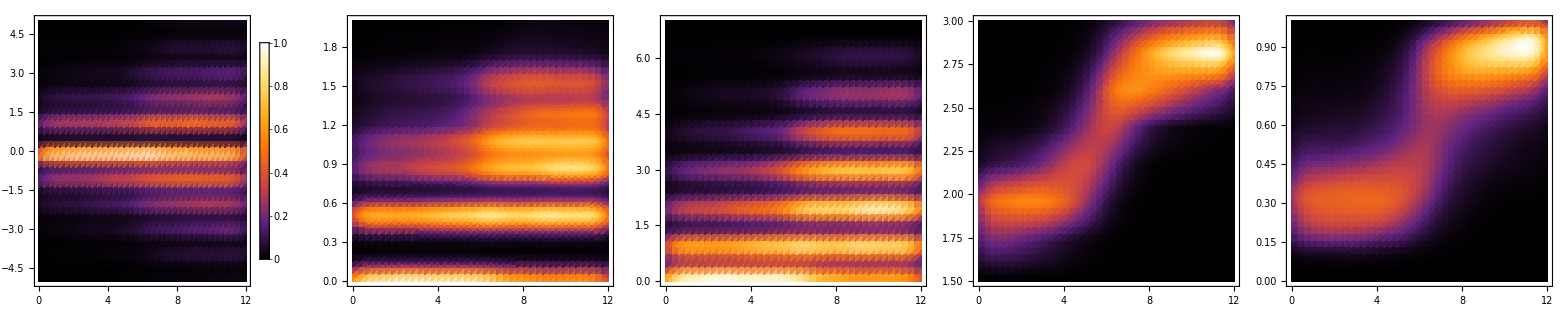

```mathematica
dpgrid = Legended[Grid[{{dpW,dpC,dpL,dpGR,dpCR}},Spacings->0.5],BarLegend[{"SunsetColors",{0,1}},LegendLayout->"Column",LegendMarkerSize->225,LabelStyle->Directive[Black,14,Bold]]]
```

```mathematica
Export["densitygrid.pdf",dpgrid,"AllowRasterization"->True,ImageSize->300,ImageResolution->300];
```

```mathematica
motifs[k_,m_]:=Transpose[{ConstantArray[k,Length[ct[k]]],Evaluate[N@(ct[k]/Total[Transpose[ct[k]]])[[All,m]]]}];
```

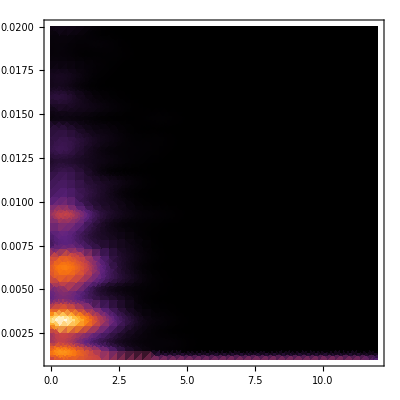

```mathematica
CTS= With[{XZ=200,YZ=200},SmoothDensityHistogram[Flatten[Table[motifs[k,1],{k,0,12,0.2}],1],Automatic,"PDF",PlotRange->{{0,12},{0.001,0.02}},Frame->True,ColorFunction->"SunsetColors",PlotTheme->"Scientific",PlotRangePadding->None,FrameTicksStyle->Directive[Black,12],ImageSize->Automatic->{XZ,YZ},Epilog->{Text[MaTeX["\\textcolor{white}{\\bf [S]}",FontSize->18],Scaled[{0.12,0.9}]],Text[MaTeX["\\textcolor{white}{\\bf \\kappa}",FontSize->18],Scaled[{0.9,0.07}]]}]]
```

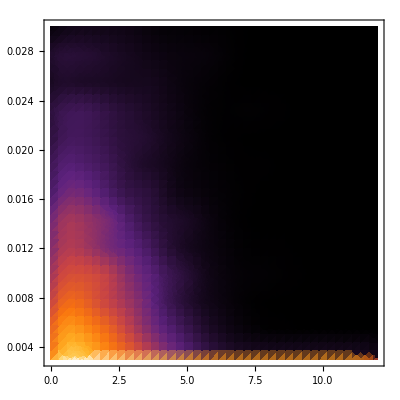

```mathematica
CTP= With[{XZ=200,YZ=200},SmoothDensityHistogram[Flatten[Table[motifs[k,2],{k,0,12,0.2}],1],Automatic,"PDF",PlotRange->{{0,12},{0.003,0.03}},Frame->True,ColorFunction->"SunsetColors",PlotTheme->"Scientific",PlotRangePadding->None,FrameTicksStyle->Directive[Black,12],ImageSize->Automatic->{XZ,YZ},Epilog->{Text[MaTeX["\\textcolor{white}{\\bf [P]}",FontSize->18],Scaled[{0.12,0.9}]],Text[MaTeX["\\textcolor{white}{\\bf \\kappa}",FontSize->18],Scaled[{0.9,0.07}]]}]]
```

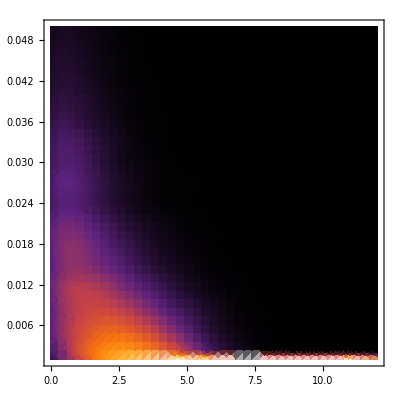

```mathematica
CTX= With[{XZ=200,YZ=200},SmoothDensityHistogram[Flatten[Table[motifs[k,3],{k,0,12,0.2}],1],Automatic,"PDF",PlotRange->{{0,12},{0.001,0.05}},Frame->True,ColorFunction->"SunsetColors",PlotTheme->"Scientific",PlotRangePadding->None,FrameTicksStyle->Directive[Black,12],ImageSize->Automatic->{XZ,YZ},Epilog->{Text[MaTeX["\\textcolor{white}{\\bf [X]}",FontSize->18],Scaled[{0.12,0.9}]],Text[MaTeX["\\textcolor{white}{\\bf \\kappa}",FontSize->18],Scaled[{0.9,0.07}]]}]]
```

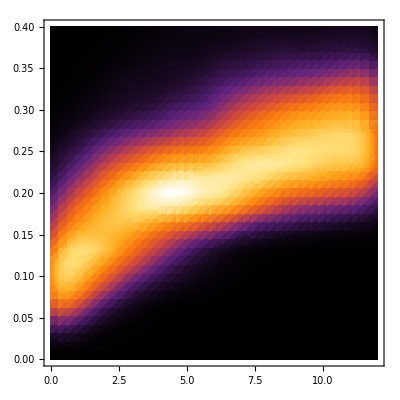

```mathematica
CTL2= With[{XZ=200,YZ=200},SmoothDensityHistogram[Flatten[Table[motifs[k,4],{k,0,12,0.2}],1],Automatic,"PDF",PlotRange->{{0,12},{0,0.4}},Frame->True,ColorFunction->"SunsetColors",PlotTheme->"Scientific",PlotRangePadding->None,FrameTicksStyle->Directive[Black,12],ImageSize->Automatic->{XZ,YZ},Epilog->{Text[MaTeX["\\textcolor{white}{\\bf [L_2]}",FontSize->18],Scaled[{0.12,0.9}]],Text[MaTeX["\\textcolor{white}{\\bf \\kappa}",FontSize->18],Scaled[{0.9,0.07}]]}]]
```

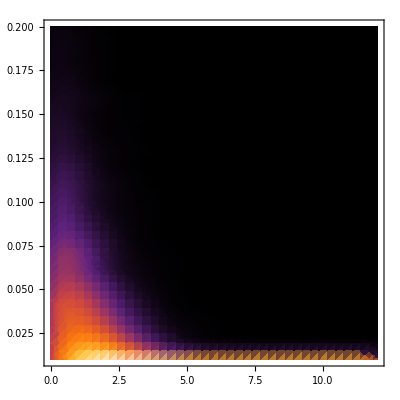

```mathematica
CTI2= With[{XZ=200,YZ=200},SmoothDensityHistogram[Flatten[Table[motifs[k,5],{k,0,12,0.2}],1],Automatic,"PDF",PlotRange->{{0,12},{0.01,0.2}},Frame->True,ColorFunction->"SunsetColors",PlotTheme->"Scientific",PlotRangePadding->None,FrameTicksStyle->Directive[Black,12],ImageSize->Automatic->{XZ,YZ},Epilog->{Text[MaTeX["\\textcolor{white}{\\bf [I_2]}",FontSize->18],Scaled[{0.12,0.9}]],Text[MaTeX["\\textcolor{white}{\\bf \\kappa}",FontSize->18],Scaled[{0.9,0.07}]]}]]
```

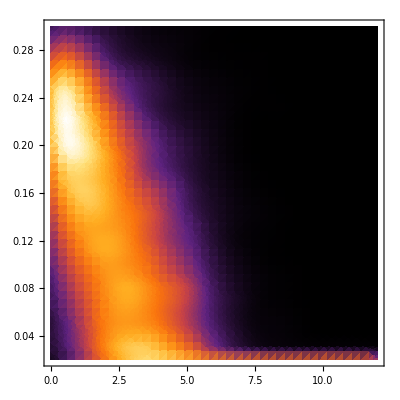

```mathematica
CTT2= With[{XZ=200,YZ=200},SmoothDensityHistogram[Flatten[Table[motifs[k,6],{k,0,12,0.2}],1],Automatic,"PDF",PlotRange->{{0,12},{0.02,0.3}},Frame->True,ColorFunction->"SunsetColors",PlotTheme->"Scientific",PlotRangePadding->None,FrameTicksStyle->Directive[Black,12],ImageSize->Automatic->{XZ,YZ},Epilog->{Text[MaTeX["\\textcolor{white}{\\bf [T_2]}",FontSize->18],Scaled[{0.12,0.9}]],Text[MaTeX["\\textcolor{white}{\\bf \\kappa}",FontSize->18],Scaled[{0.9,0.07}]]}]]
```

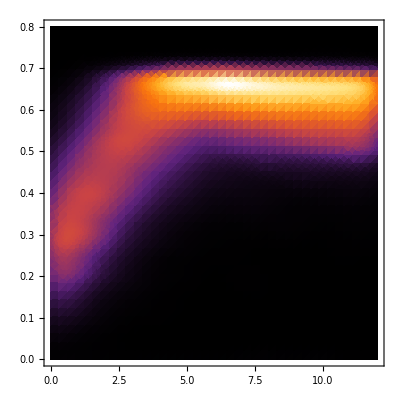

```mathematica
CTT3= With[{XZ=200,YZ=200},SmoothDensityHistogram[Flatten[Table[motifs[k,7],{k,0,12,0.2}],1],Automatic,"PDF",PlotRange->{{0,12},{0,0.8}},Frame->True,ColorFunction->"SunsetColors",PlotTheme->"Scientific",PlotRangePadding->None,FrameTicksStyle->Directive[Black,12],ImageSize->Automatic->{XZ,YZ},Epilog->{Text[MaTeX["\\textcolor{white}{\\bf [T_3]}",FontSize->18],Scaled[{0.12,0.9}]],Text[MaTeX["\\textcolor{white}{\\bf \\kappa}",FontSize->18],Scaled[{0.9,0.07}]]}]]
```

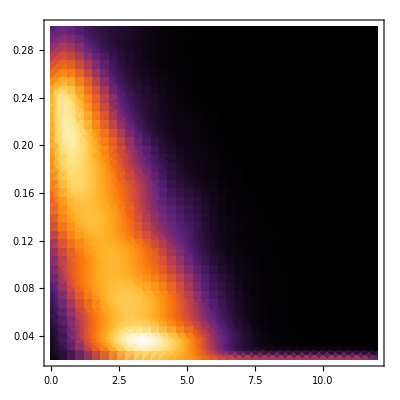

```mathematica
CTI3= With[{XZ=200,YZ=200},SmoothDensityHistogram[Flatten[Table[motifs[k,8],{k,0,12,0.2}],1],Automatic,"PDF",PlotRange->{{0,12},{0.02,0.3}},Frame->True,ColorFunction->"SunsetColors",PlotTheme->"Scientific",PlotRangePadding->None,FrameTicksStyle->Directive[Black,12],ImageSize->Automatic->{XZ,YZ},Epilog->{Text[MaTeX["\\textcolor{white}{\\bf [I_3]}",FontSize->18],Scaled[{0.12,0.9}]],Text[MaTeX["\\textcolor{white}{\\bf \\kappa}",FontSize->18],Scaled[{0.9,0.07}]]}]]
```

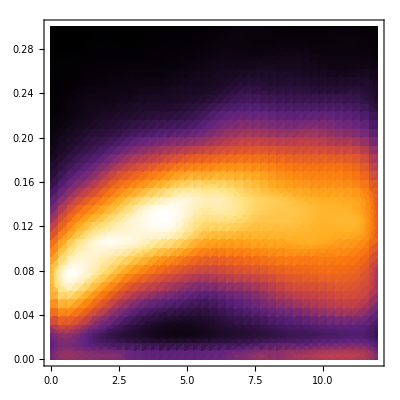

```mathematica
CTI4= With[{XZ=200,YZ=200},SmoothDensityHistogram[Flatten[Table[motifs[k,9],{k,0,12,0.2}],1],Automatic,"PDF",PlotRange->{{0,12},{0,0.3}},Frame->True,ColorFunction->"SunsetColors",PlotTheme->"Scientific",PlotRangePadding->None,FrameTicksStyle->Directive[Black,12],ImageSize->Automatic->{XZ,YZ},Epilog->{Text[MaTeX["\\textcolor{white}{\\bf [I_4]}",FontSize->18],Scaled[{0.12,0.9}]],Text[MaTeX["\\textcolor{white}{\\bf \\kappa}",FontSize->18],Scaled[{0.9,0.07}]]}]]
```

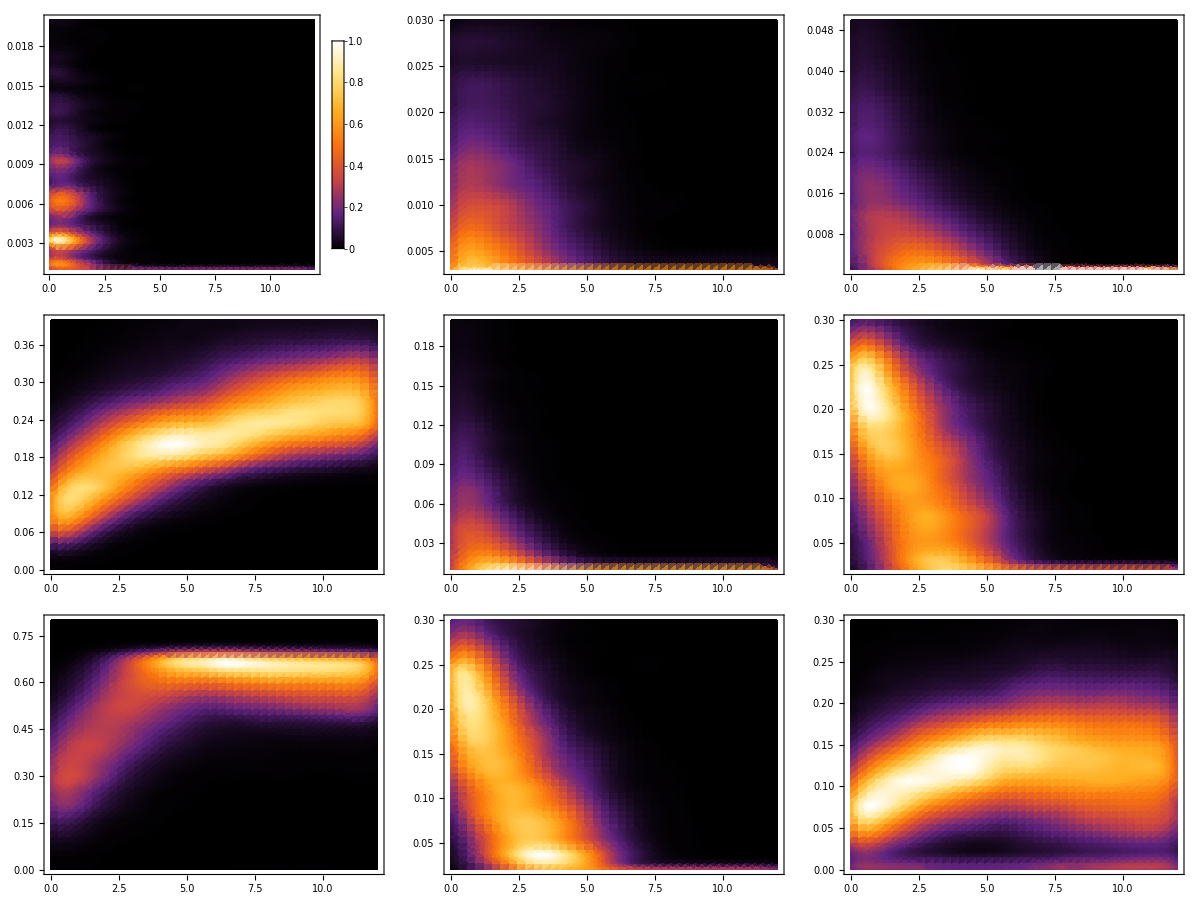

```mathematica
ctgrid = Legended[Grid[{{CTS,CTP,CTX},{CTL2,CTI2,CTT2},{CTT3,CTI3,CTI4}},Spacings->0.3],BarLegend[{"SunsetColors",{0,1}},LegendLayout->"Column",LegendMarkerSize->550,LabelStyle->Directive[Black,20,Bold]]]
```

```mathematica
Export["CTgridN10.pdf",ctgrid,"AllowRasterization"->True,ImageSize->300,ImageResolution->300];
```

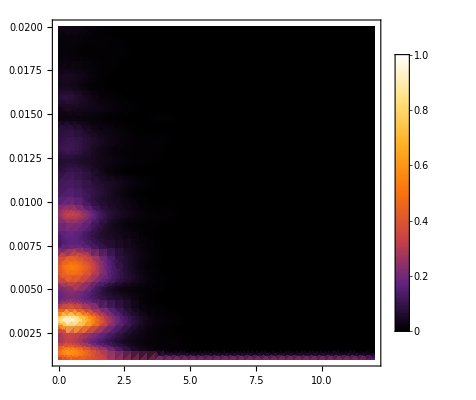
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- |

```mathematica
ctgrid2 = Legended[Grid[{{CTS,CTP,CTX,CTL2,CTI2},{CTT2,CTT3,CTI3,CTI4}},Spacings->0.3],BarLegend[{"SunsetColors",{0,1}},LegendLayout->"Column",LegendMarkerSize->450,LabelStyle->Directive[Black,20,Bold]]]
```

```mathematica
Export["CTgridlongN10.pdf",ctgrid2,"AllowRasterization"->True,ImageSize->300,ImageResolution->300];
```